```mathematica
gauss[x_,sigma_]:=(1/(sigma*Sqrt[2*Pi]))Exp[-0.5(x/sigma)^2]
```

```mathematica
res=10;
```

```mathematica
resample[x_,y_,d_]:=Sum[d[[u,v]]*gauss[Norm[{u-x,v-y}]],{u,1,res},{v,1,res}]
```

```mathematica
f[x_,y_,p_]:=Sum[{x,y}+gauss[Norm[{u-x,v-y}]*p[[u*res+1,v*res+1]],0.1],{u,0,1,1/res},{v,0,1,1/res}]
```

```mathematica
idMap=Table[{0, 0},{u, 0, 1, 1/res}, {v, 0, 1, 1/res}];
```

```mathematica
idMap[[1,1]]
```

{0,0}

```mathematica
idMap[[11,11]]
f[1,1,idMap]
f[a,b,idMap]
```

{0,0}

{603.72,603.72}

{482.72+121 a,482.72+121 b}

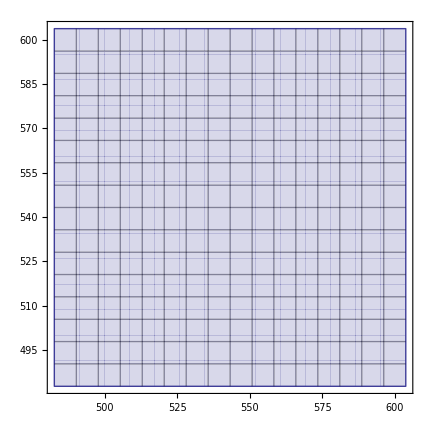

```mathematica
ParametricPlot[f[x,y,idMap],{x,0,1},{y,0,1}]
```